```mathematica
Clear["`*"]
```

```mathematica
data=Developer`ReadRawJSONString/@Import["/home/bczhc/xdo-rec/2023-03-19 18:14:40","List"]//Parallelize;
```

```mathematica
locations={#["x"],#["y"]}&/@Select[#["event"]&/@data,#["type"]=="MouseMotion"&]
```

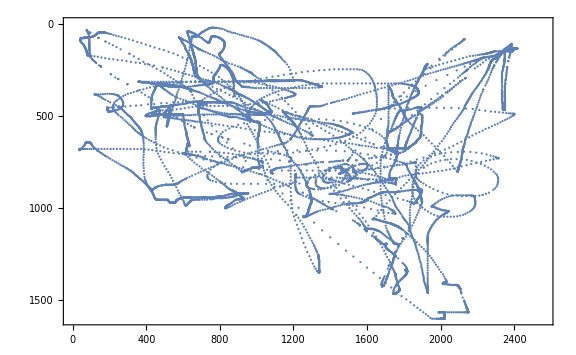

```mathematica
ListPlot[locations,PlotRange->{{0,2560},{0,1600}},ScalingFunctions->"Reverse",ImageSize->Large,Frame->True]
```

```mathematica
Total[EuclideanDistance[{0,0},N@#]&/@Differences[locations]]/2560*3.3/100
```

0.939686